# Plasma Taxonomy

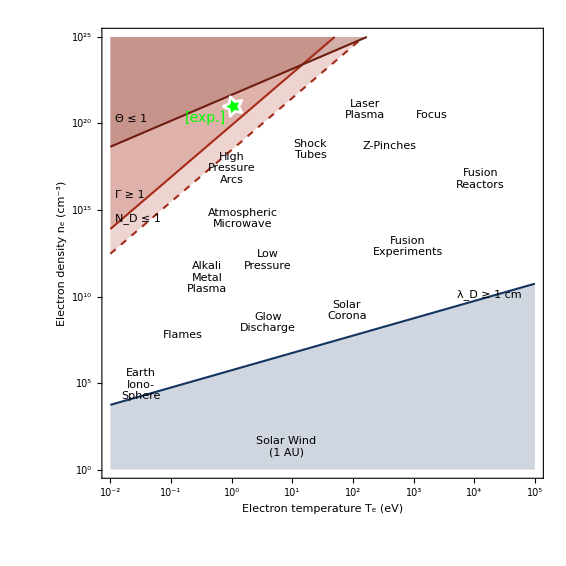

```mathematica
Block[{ϵ0,e,λD,Te, ne,ℏ,me,EF,DL,DN,CP,DG,idx,dt,clr1,clr2,clr3,star,gf1,coord,lb,gf2,gf},

(* -- Debye length -- *)
ϵ0=8.854*^-12;
e=1.6*^-19;

λD=Sqrt[(ϵ0 Te)/(ne e)];
ℏ=1.055*^-34;
me=9.109*^-31;
EF=(ℏ^2/(2me))(3 π^2 ne)^(2/3);


DL=ne/.Solve[λD==.01,ne];
DN=ne/.Solve[(4π/3) ne λD^3==1,ne];
CP=ne/.Solve[e^2/(4π ϵ0 e Te)(4π ne/3)^(1/3)==1,ne];
DG=ne/.Solve[(e Te)/EF==1,ne]; (* degeneracy *)

(* -- data to plot -- *)
idx=PowerRange[10^-2,10^5,10^.5];
dt={
Table[{Log10[i],Log10[1*^-6 DL/.Te->i][[1]]},{i,idx}],
Table[{Log10[i],Log10[1*^-6 DN/.Te->i][[1]]},{i,idx}],
Table[{Log10[i],Log10[1*^-6 CP/.Te->i][[1]]},{i,idx}],
Table[{Log10[i],Log10[1*^-6 DG/.Te->i][[1]]},{i,idx}]
}; (* [cm^-3] *)

(* -- colors -- *)
clr1=RGBColor[{19,52,95}/255];
clr2=RGBColor[{165,42,23}/255];
clr3=RGBColor[{110,28,15.3}/255];

(* -- star mark -- *)
star=Graphics[{EdgeForm[Directive[White,AbsoluteThickness[2]]],FaceForm[Green],Polygon[Table[(Mod[k,2]+1){Cos[2π k/10],Sin[2π k/10]},{k,10}]]}];

(* -- plot outline -- *)
gf1=ListPlot[

dt,

Epilog->{
(* -- label criteria -- *)
{Text[Framed[Style["λ_D ≥ 1 cm",{FontColor->clr1,FontSize->14,FontWeight->Plain}],Background->Transparent,FrameStyle->None],
Scaled[{.95,.42}],{1,1},{1,.28}]},
{Text[Framed[Style[StringForm["`1` ≤ 1",Style[Subscript[Style["N",Italic],"D"]]],{FontColor->clr2,FontSize->14,FontWeight->Plain}],Background->Transparent,FrameStyle->None],
Scaled[{.03,.59}],{-1,1},{1,.84}]},
{Text[Framed[Style["Γ ≥ 1",{FontColor->clr2,FontSize->14,FontWeight->Plain}],Background->Transparent,FrameStyle->None],
Scaled[{.03,.64}],{-1,1},{1,.84}]},
{Text[Framed[Style["Θ ≤ 1",{FontColor->clr3,FontSize->14,FontWeight->Plain}],Background->Transparent,FrameStyle->None],
Scaled[{.03,.81}],{-1,1},{1,.42}]},
(* -- experiment condition -- *)
Inset[star,{0,21},{0,0},Offset[20]],
{Text[Style["[exp.]",{FontColor->Green,FontSize->14,FontWeight->Plain}],
{-.1,20.3},{1,0}]}
},

Joined->True,
PlotRange->{{-2,5},{0,25}},
PlotRangePadding->0,

PlotStyle->{
{clr1,AbsoluteThickness[1.5]},
{clr2,AbsoluteThickness[1.5],AbsoluteDashing[5]},
{clr2,AbsoluteThickness[1.5]},
{clr3,AbsoluteThickness[1.5]}
},

Axes->False,
Frame->True,
FrameLabel->{{StringForm["Electron density `1` (cm^-3)",Subscript[Style["n",Italic],"e"]],None},{StringForm["Electron temperature `1` (eV)",Subscript[Style["T",Italic],"e"]],None}},
FrameTicks->{
{Table[{i,If[Mod[i,5]==0,Superscript[10,i],Null],{If[Mod[i,5]==0,.015,.008],0}},{i,0,25,1}],Table[{i,Null,{If[Mod[i,5]==0,.015,.008],0}},{i,0,25,1}]},
{Table[{i,Superscript[10,i],{.015,0}},{i,-2,5,1}],Table[{i,Null,{.015,0}},{i,-2,5,1}]}
},
FrameStyle->Directive[Black,AbsoluteThickness[1]],

LabelStyle->{FontColor->Black,FontFamily->"Arial",FontSize->14,FontWeight->Plain},

GridLines->None,

PlotRangeClipping->False,
(*ImagePadding->{{85,20},{65,15}},*)
ImageSize->(100*2)*(72/25.4),
AspectRatio->1,

Filling->{{1-> Bottom},{2->Top},{3->Top},{4->Top}}

];

(* -- rectangle text boxes -- *)
coord={{2.2,20.8},{3.3,20.5},{0,17.4},{.18,14.5},{1.3,18.5},{2.6,18.7},{4.1,16.8},{-0.4,11.1},{0.6,12.1},{2.9,12.9},{-0.8,7.8},{0.6,8.5},{1.9,9.2},{-1.5,4.9},{0.9,1.3},{2.9,1.3}};
lb={"Laser\nPlasma","Focus","High\nPressure\nArcs","Atmospheric\nMicrowave","Shock\nTubes","Z-Pinches","Fusion\nReactors","Alkali\nMetal\nPlasma","Low\nPressure","Fusion\nExperiments","Flames","Glow\nDischarge","Solar\nCorona","Earth\nIono-\nSphere","Solar Wind\n(1 AU)","Earth\nPlasma sheet"};

gf2=Graphics@Table[
Text[
Framed[
Style[lb[[i]],{FontColor->Gray,FontFamily->"Arial",FontSize->14}],
FrameStyle->Directive[Gray,AbsoluteThickness[1]],Background->White],
coord[[i]]],
{i, 15}];

gf = Show[gf1,gf2];

Print[gf];
Export[NotebookDirectory[]<>"taxonomy.pdf", gf];

];
```